```mathematica
the results are independent of the setting of θ1,Ld1,LB,k1.
```

```mathematica
tt={};Do[ θ1=1;θ2=-2θ1;Ld1=1;LB=1;   ρ1=LB/θ1; ρ2=LB/θ2 ;ρ3=LB/θ3;ρ4= LB/θ4;   θ4=-(θ1+θ2+θ3);Ld3=Simplify[(-Ld1 θ1-Ld2 θ1-Ld2 θ2)/(θ1+θ2+θ3)];  ρ2p=-ρ2; θ2p=-θ2;ρ4p=-ρ4; θ4p=-θ4;bR56=1/48 (24 Ld1 θ1 θ2 );
cR56=Simplify[1/2 (Ld2 (θ1+θ2) θ3+Ld1 θ1 (2 θ2+θ3))];
dR56=Simplify[Ld3 (θ1+θ2+θ3) θ4+Ld2 (θ1+θ2) (θ3+θ4)+Ld1 θ1 (θ2+θ3+θ4)];h=N[(1-C1)/(C1 dR56)];
k1=1;k2=N[k1/(1+bR56 h)^(4/3)];
k3=N[k1/(1+cR56 h)^(4/3)];

k4=N[k1 C1^(4/3)];
eq1=(Ld1 (-k1 θ1^2 θ2 ρ1^(1/3)+k2 θ1 θ2^2 ρ2p^(1/3)))/(2 (θ1+θ2))+(Ld3 (k1 θ1^2 θ3 ρ1^(1/3)+k2 θ2p (2 θ1+θ2) θ3 ρ2p^(1/3)+k3 (θ1+θ2) θ3^2 ρ3^(1/3)))/(2 (θ1+θ2));
eq2=Ld1 (-k1 θ1^2 θ2 ρ1^(1/3)+k2 θ1 θ2^2 ρ2p^(1/3))+Ld3 ( k3 θ3^2 ( θ4) ρ3^(1/3)-k4 θ3 (θ4)^2 ρ4p^(1/3) ); 
root=FindRoot[eq1==0&&eq2==0,{{θ3,1.5θ1},{Ld2 ,1.2Ld1}}];
AppendTo[tt,{C1, θ3/θ1/.root, θ4/θ1/.root,Ld2/Ld1/.root,Ld3/Ld1/.root}],{C1,4,50,1}]
```

{10,1.502,-0.502003,1.18615,0.370821}

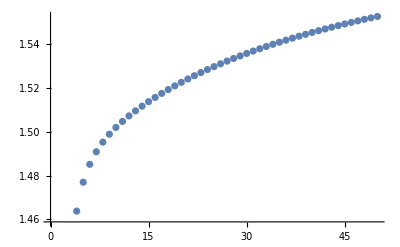

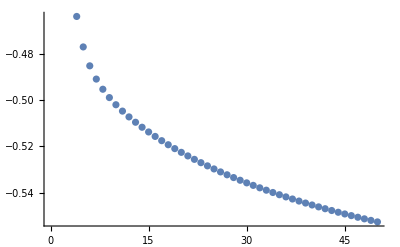

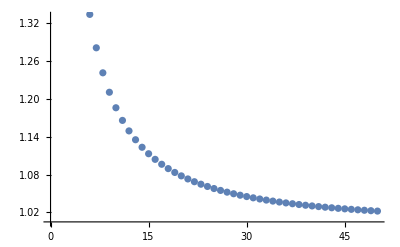

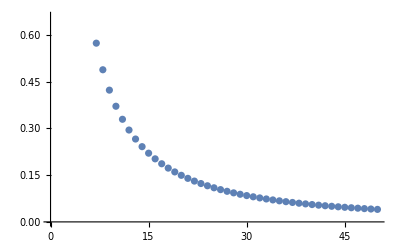

```mathematica
tt[[7]]
factor=Transpose[tt][[1]];
θ3vsC=Transpose[tt][[2]];
θ4vsC=Transpose[tt][[3]];
Ld2vsC=Transpose[tt][[4]];
Ld3vsC=Transpose[tt][[5]];
ListPlot[Transpose[{factor,θ3vsC}]]
ListPlot[Transpose[{factor,θ4vsC}]]
ListPlot[Transpose[{factor,Ld2vsC}]]
ListPlot[Transpose[{factor,Ld3vsC}]]
```